```mathematica
SetDirectory["~/Documents/School Stuff/MSU/PHY989/PHY989-Project-1/"];
data=Import["data.txt","Table"];
data2 = Import["potential.txt","Table"];
```

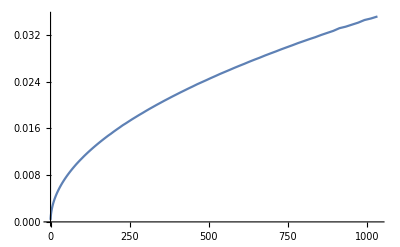

```mathematica
ListLinePlot[data,PlotRange->All]
(*ListPlot3D[data2,PlotRange->All]*)
```

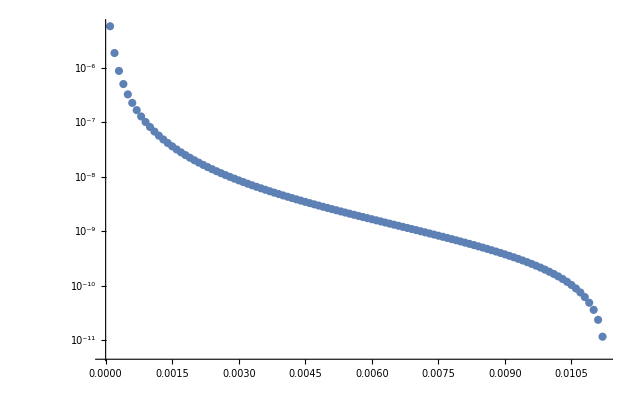

-0.0000243192

{ | DF | SS | MS | F-Statistic | P-Value
1/x | 1 | 3.35084×10^-11 | 3.35084×10^-11 | 1201.88 | 2.84312×10^-86
Error | 199 | 5.5481×10^-12 | 2.78799×10^-14 |  | 
Total | 200 | 3.90565×10^-11 |  |  | ,0.857947}

```mathematica
(*fit = LinearModelFit[data,{1/x},x, IncludeConstantBasis->False];
fitted= Table[{i*k0,fit[i*k0]},{i,1,npoints}];
Show[ListLogPlot[data,PlotRange->All],ListLinePlot[fitted,PlotRange->All]]
δ = (180/Pi)*ArcTan[-m*fit["BestFitParameters"][[1]]]
fit[{"ANOVATable","RSquared"}]*)
```